```mathematica
(* We'll use ** as a noncommutative multiply that knows multiplication by 0 is 0 *)
```

```mathematica
Unprotect[NonCommutativeMultiply];
Clear[NonCommutativeMultiply];
NonCommutativeMultiply[___,0,___]:=0
NonCommutativeMultiply[a___,b_Plus,c___]:=Distribute[NCM[a,b,c]]/.NCM->NonCommutativeMultiply
NonCommutativeMultiply[a___,-1,b___]:=-1a**b
NonCommutativeMultiply[-1,a___,b___]:=-1a**b
NonCommutativeMultiply[a___,b___,-1]:=-1a**b
Protect[NonCommutativeMultiply];
```

```mathematica
(* But not this version that factors out all numbers so that we can keep 1 as a matrix *)
```

```mathematica
(*Unprotect[NonCommutativeMultiply];
Clear[NonCommutativeMultiply]
(*Factor out numerics-- could generalize to some ScalarQ*)
nc:NonCommutativeMultiply[a__]/;MemberQ[{a},_?NumericQ]:=NCMFactorNumericQ[NCM[a]]/.NCM->NonCommutativeMultiply
(*Simplify Powers*)
b___**a_^n_.**a_^m_.**c___:=NCM[b,a^(n+m),c]/.NCM->NonCommutativeMultiply
(*Expand Brackets*)
nc:NonCommutativeMultiply[a___,b_Plus,c___]:=Distribute[NCM[a,b,c]]/.NCM->NonCommutativeMultiply
(*Sort Subscripts*)
c___**Subscript[a_,i_]**Subscript[b_,j_]**d___/;i>j:=c**Subscript[b,j]**Subscript[a,i]**d
Protect[NonCommutativeMultiply];

Unprotect[NCM];
Clear[NCM]
NCMFactorNumericQ[nc_NCM]:=With[{pos=Position[nc,_?NumericQ,1]},Times@@Extract[nc,pos] Delete[nc,pos]]
NCM[a_]:=a
NCM[]:=1
Protect[NCM];*)
```

## Volume term

```mathematica
volTerm=Sum[λ/96LeviCivitaTensor[4][[μ,ν,ρ,σ]]g5**eslash[μ][x]**eslash[ν][x]**eslash[ρ][x]**eslash[σ][x],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}]
```

1/96 λ g5**eslash[1][x]**eslash[2][x]**eslash[3][x]**eslash[4][x]-1/96 λ g5**eslash[1][x]**eslash[2][x]**eslash[4][x]**eslash[3][x]-1/96 λ g5**eslash[1][x]**eslash[3][x]**eslash[2][x]**eslash[4][x]+1/96 λ g5**eslash[1][x]**eslash[3][x]**eslash[4][x]**eslash[2][x]+1/96 λ g5**eslash[1][x]**eslash[4][x]**eslash[2][x]**eslash[3][x]-1/96 λ g5**eslash[1][x]**eslash[4][x]**eslash[3][x]**eslash[2][x]-1/96 λ g5**eslash[2][x]**eslash[1][x]**eslash[3][x]**eslash[4][x]+1/96 λ g5**eslash[2][x]**eslash[1][x]**eslash[4][x]**eslash[3][x]+1/96 λ g5**eslash[2][x]**eslash[3][x]**eslash[1][x]**eslash[4][x]-1/96 λ g5**eslash[2][x]**eslash[3][x]**eslash[4][x]**eslash[1][x]-1/96 λ g5**eslash[2][x]**eslash[4][x]**eslash[1][x]**eslash[3][x]+1/96 λ g5**eslash[2][x]**eslash[4][x]**eslash[3][x]**eslash[1][x]+1/96 λ g5**eslash[3][x]**eslash[1][x]**eslash[2][x]**eslash[4][x]-1/96 λ g5**eslash[3][x]**eslash[1][x]**eslash[4][x]**eslash[2][x]-1/96 λ g5**eslash[3][x]**eslash[2][x]**eslash[1][x]**eslash[4][x]+1/96 λ g5**eslash[3][x]**eslash[2][x]**eslash[4][x]**eslash[1][x]+1/96 λ g5**eslash[3][x]**eslash[4][x]**eslash[1][x]**eslash[2][x]-1/96 λ g5**eslash[3][x]**eslash[4][x]**eslash[2][x]**eslash[1][x]-1/96 λ g5**eslash[4][x]**eslash[1][x]**eslash[2][x]**eslash[3][x]+1/96 λ g5**eslash[4][x]**eslash[1][x]**eslash[3][x]**eslash[2][x]+1/96 λ g5**eslash[4][x]**eslash[2][x]**eslash[1][x]**eslash[3][x]-1/96 λ g5**eslash[4][x]**eslash[2][x]**eslash[3][x]**eslash[1][x]-1/96 λ g5**eslash[4][x]**eslash[3][x]**eslash[1][x]**eslash[2][x]+1/96 λ g5**eslash[4][x]**eslash[3][x]**eslash[2][x]**eslash[1][x]

```mathematica
D[volTerm,eslash[1][x]]
```

1/96 λ g5**1**eslash[2][x]**eslash[3][x]**eslash[4][x]-1/96 λ g5**1**eslash[2][x]**eslash[4][x]**eslash[3][x]-1/96 λ g5**1**eslash[3][x]**eslash[2][x]**eslash[4][x]+1/96 λ g5**1**eslash[3][x]**eslash[4][x]**eslash[2][x]+1/96 λ g5**1**eslash[4][x]**eslash[2][x]**eslash[3][x]-1/96 λ g5**1**eslash[4][x]**eslash[3][x]**eslash[2][x]-1/96 λ g5**eslash[2][x]**1**eslash[3][x]**eslash[4][x]+1/96 λ g5**eslash[2][x]**1**eslash[4][x]**eslash[3][x]+1/96 λ g5**eslash[2][x]**eslash[3][x]**1**eslash[4][x]-1/96 λ g5**eslash[2][x]**eslash[3][x]**eslash[4][x]**1-1/96 λ g5**eslash[2][x]**eslash[4][x]**1**eslash[3][x]+1/96 λ g5**eslash[2][x]**eslash[4][x]**eslash[3][x]**1+1/96 λ g5**eslash[3][x]**1**eslash[2][x]**eslash[4][x]-1/96 λ g5**eslash[3][x]**1**eslash[4][x]**eslash[2][x]-1/96 λ g5**eslash[3][x]**eslash[2][x]**1**eslash[4][x]+1/96 λ g5**eslash[3][x]**eslash[2][x]**eslash[4][x]**1+1/96 λ g5**eslash[3][x]**eslash[4][x]**1**eslash[2][x]-1/96 λ g5**eslash[3][x]**eslash[4][x]**eslash[2][x]**1-1/96 λ g5**eslash[4][x]**1**eslash[2][x]**eslash[3][x]+1/96 λ g5**eslash[4][x]**1**eslash[3][x]**eslash[2][x]+1/96 λ g5**eslash[4][x]**eslash[2][x]**1**eslash[3][x]-1/96 λ g5**eslash[4][x]**eslash[2][x]**eslash[3][x]**1-1/96 λ g5**eslash[4][x]**eslash[3][x]**1**eslash[2][x]+1/96 λ g5**eslash[4][x]**eslash[3][x]**eslash[2][x]**1

```mathematica
Length[D[volTerm,eslash[1][x]]]
```

24

## Curvature term

```mathematica
P[μ_,ν_,x_]:=U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]
```

```mathematica
D[Sum[P[μ,ν,x+xi hat[μ]+yi hat[ν]],{xi,-stencil,stencil},{yi,-1,1}],U[μ][x]]
```

1**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]

```mathematica
Pdag[μ_,ν_,x_]:=U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]
```

```mathematica
Pdag[μ,ν,x]-P[ν,μ,x]
```

0

```mathematica
(* P[-μ,ν,x] = Pdag[μ,ν,x-hat[μ]] *)
```

```mathematica
(* P[μ,-ν,x] = Pdag[μ,ν,x-hat[ν]] *)
```

```mathematica
(* P[-μ,-ν,x] = P[μ,ν,x-hat[μ]-hat[ν]] *)
```

```mathematica
G[μ_,ν_,x_]:=1/8(P[μ,ν,x]-Pdag[μ,ν,x-hat[μ]]-Pdag[μ,ν,x-hat[ν]]+P[μ,ν,x-hat[μ]-hat[ν]]-Pdag[μ,ν,x]+P[μ,ν,x-hat[μ]]+P[μ,ν,x-hat[ν]]-Pdag[μ,ν,x-hat[μ]-hat[ν]])
```

```mathematica
Gtimes8[μ_,ν_,x_]:=(P[μ,ν,x]-Pdag[μ,ν,x-hat[μ]]-Pdag[μ,ν,x-hat[ν]]+P[μ,ν,x-hat[μ]-hat[ν]]-Pdag[μ,ν,x]+P[μ,ν,x-hat[μ]]+P[μ,ν,x-hat[ν]]-Pdag[μ,ν,x-hat[μ]-hat[ν]])
```

```mathematica
Gtimes8p[μ_,ν_,x_]:=(P[μ,ν,x]+P[μ,ν,x-hat[μ]-hat[ν]]+P[μ,ν,x-hat[μ]]+P[μ,ν,x-hat[ν]])
```

```mathematica
Gtimes8m[μ_,ν_,x_]:=(Pdag[μ,ν,x-hat[μ]]+Pdag[μ,ν,x-hat[ν]]+Pdag[μ,ν,x]+Pdag[μ,ν,x-hat[μ]-hat[ν]])
```

```mathematica
stencil=2;
```

```mathematica
Expand[D[Sum[G[μ,ν,x+xi hat[μ]+yi hat[ν]],{xi,-stencil,stencil},{yi,-stencil,stencil}],U[μ][x]]]
```

1/2 1**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]-1/2 U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]

```mathematica
Expand[D[Sum[G[μ,ν,x+xi hat[μ]+yi hat[ν]]eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{xi,-stencil,stencil},{yi,-stencil,stencil}],U[μ][x]]]
```

1/8 eslashPart[ρ,σ,x] 1**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]+1/8 eslashPart[ρ,σ,x+hat[μ]] 1**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]+1/8 eslashPart[ρ,σ,x+hat[ν]] 1**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]+1/8 eslashPart[ρ,σ,x+hat[μ]+hat[ν]] 1**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]-1/8 eslashPart[ρ,σ,x] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]-1/8 eslashPart[ρ,σ,x+hat[μ]] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]-1/8 eslashPart[ρ,σ,x-hat[ν]] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]-1/8 eslashPart[ρ,σ,x+hat[μ]-hat[ν]] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]

```mathematica
Expand[D[D[Sum[Sum[κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]]G[μ,ν,x+xi hat[μ]+yi hat[ν]]eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{xi,-stencil,stencil},{yi,-stencil,stencil}],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],U[1][x]],eslashPart[3,4,x]]]
```

1/64 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]-1/64 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]

```mathematica
fullThing=Expand[D[Sum[Sum[κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]- 0 κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{xi,-stencil,stencil},{yi,-stencil,stencil}],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],U[1][x]]]
```

1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x]+1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]]+1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[2]]+1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]+hat[2]]-1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[4,3,x]-1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[4,3,x+hat[1]]-1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[4,3,x+hat[2]]-1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[4,3,x+hat[1]+hat[2]]-1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[2,4,x]-1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[2,4,x+hat[1]]-1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[2,4,x+hat[3]]-1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[2,4,x+hat[1]+hat[3]]+1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[4,2,x]+1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[4,2,x+hat[1]]+1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[4,2,x+hat[3]]+1/128 κ 1**U[3][x+hat[1]]**Udag[1][x+hat[3]]**Udag[3][x]**eslashPart[4,2,x+hat[1]+hat[3]]+1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[2,3,x]+1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[2,3,x+hat[1]]+1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[2,3,x+hat[4]]+1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[2,3,x+hat[1]+hat[4]]-1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[3,2,x]-1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[3,2,x+hat[1]]-1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[3,2,x+hat[4]]-1/128 κ 1**U[4][x+hat[1]]**Udag[1][x+hat[4]]**Udag[4][x]**eslashPart[3,2,x+hat[1]+hat[4]]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x+hat[1]]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x-hat[2]]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x+hat[1]-hat[2]]+1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[4,3,x]+1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[4,3,x+hat[1]]+1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[4,3,x-hat[2]]+1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[4,3,x+hat[1]-hat[2]]+1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[2,4,x]+1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[2,4,x+hat[1]]+1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[2,4,x-hat[3]]+1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[2,4,x+hat[1]-hat[3]]-1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[4,2,x]-1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[4,2,x+hat[1]]-1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[4,2,x-hat[3]]-1/128 κ U[3][x-hat[3]]**1**Udag[3][x+hat[1]-hat[3]]**Udag[1][x-hat[3]]**eslashPart[4,2,x+hat[1]-hat[3]]-1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[2,3,x]-1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[2,3,x+hat[1]]-1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[2,3,x-hat[4]]-1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[2,3,x+hat[1]-hat[4]]+1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[3,2,x]+1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[3,2,x+hat[1]]+1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[3,2,x-hat[4]]+1/128 κ U[4][x-hat[4]]**1**Udag[4][x+hat[1]-hat[4]]**Udag[1][x-hat[4]]**eslashPart[3,2,x+hat[1]-hat[4]]

```mathematica
Length[fullThing]
```

48

```mathematica
impLevi=ExpandAll[D[Sum[Sum[κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{xi,-stencil,stencil},{yi,-stencil,stencil}],{μ,1,4},{ν,μ+1,4},{ρ,ν+1,4},{σ,ρ+1,4}],U[1][x]]]
```

1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x]+1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]]+1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[2]]+1/128 κ 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]+hat[2]]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x+hat[1]]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x-hat[2]]-1/128 κ U[2][x-hat[2]]**1**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x+hat[1]-hat[2]]

```mathematica
impLeviSym=impLevi/.{hat[1]->hat[μ],2->ν,3->ρ,4->σ};
```

```mathematica
Print["Curvature term staples"];Do[Print["Term ",n];Print[epsilon[ν,ρ,σ]impLeviSym[[n]]];Print[""];,{n,Length[impLevi]}];
```

Curvature term staples

Term 1

1/128 κ epsilon[ν,ρ,σ] 1**U[ν][x+hat[μ]]**Udag[1][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 2

1/128 κ epsilon[ν,ρ,σ] 1**U[ν][x+hat[μ]]**Udag[1][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 3

1/128 κ epsilon[ν,ρ,σ] 1**U[ν][x+hat[μ]]**Udag[1][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 4

1/128 κ epsilon[ν,ρ,σ] 1**U[ν][x+hat[μ]]**Udag[1][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 5

-1/128 κ epsilon[ν,ρ,σ] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[1][x-hat[ν]]**eslashPart[ρ,σ,x]

Term 6

-1/128 κ epsilon[ν,ρ,σ] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[1][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]

Term 7

-1/128 κ epsilon[ν,ρ,σ] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[1][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]

Term 8

-1/128 κ epsilon[ν,ρ,σ] U[ν][x-hat[ν]]**1**Udag[ν][x+hat[μ]-hat[ν]]**Udag[1][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]

```mathematica
128/8
```

16

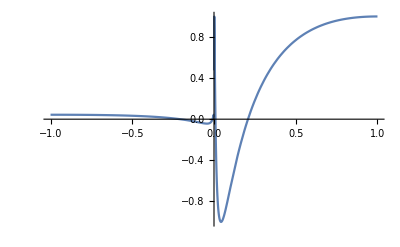

```mathematica
Plot[Re[x^I],{x,-1,1}]
```

```mathematica
TrigToExp[(-1)^I]
```

(-1)^ⅈ

```mathematica
ExpToTrig[(-1)^I]
```

Cosh[π]-Sinh[π]

```mathematica
Cosh[1.0 π]
```

11.592

```mathematica
Sinh[1.0 π]
```

11.5487

```mathematica
1.0(Cosh[π]-Sinh[π])
```

0.0432139

```mathematica
1.0 Exp[-π]
```

0.0432139

```mathematica
Log[Abs[1/2κ]]
```

```mathematica
Assuming[x>0,FullSimplify[Re[x^I]]]
```

Re[x^ⅈ]

```mathematica
Assuming[x>0,ExpToTrig[Re[x^I]]]
```

Re[x^ⅈ]

```mathematica
Assuming[x>0,TrigToExp[Re[x^I]]]
```

Re[x^ⅈ]

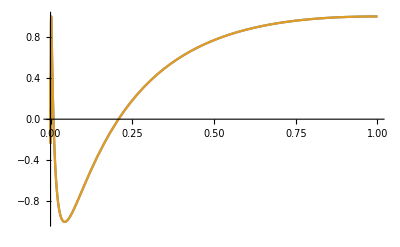

```mathematica
Plot[{Re[x^I],Cos[Log[x]]},{x,0,1}]
```

```mathematica
1/(2k)-3
```

```mathematica
Log[1/2(1/2)(m-2)]
```

```mathematica
1/
```

```mathematica
γ1DP
```

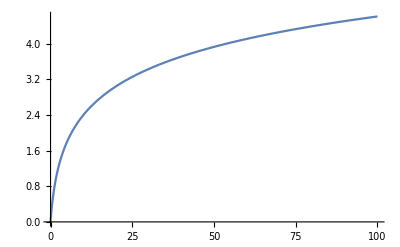

```mathematica
Plot[Log[1+m],{m,0,100}]
```

## R^2 term

```mathematica
(* Here is the toy version *)
```

```mathematica
a**U**U+b**U
```

b**U+a**U**U

```mathematica
1/2D[a**U**U+b**U,{U,2}]/.{1**p_:>U**p}/.{p_**1:>p**U}
```

a**U**U

```mathematica
D[a**U**U+b**U,U]/.{1**p_:>U**p}/.{p_**1:>p**U}
```

b**U+2 a**U**U

```mathematica
(D[a**U**U+b**U,U]/.{1**p_:>U**p}/.{p_**1:>p**U})-(1/2D[a**U**U+b**U,{U,2}]/.{1**p_:>U**p}/.{p_**1:>p**U})
```

b**U+a**U**U

```mathematica
(D[a**U**U+b**U,U]-1/2D[a**U**U+b**U,{U,2}])/.{1**p_:>U**p}/.{p_**1:>p**U}
```

b**U+a**U**U

```mathematica
(* checking Rterm reconstruction *)
```

```mathematica
Rterm=Expand[Sum[Sum[κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]- κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{xi,-stencil+1,stencil-1},{yi,-stencil+1,stencil-1}],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}]];
```

```mathematica
Dimensions[Rterm]
```

{864}

```mathematica
RfullThing=Expand[D[Sum[Sum[κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]- κ/2(1/8)LeviCivitaTensor[4][[μ,ν,ρ,σ]](1/8)Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{xi,-stencil,stencil},{yi,-stencil,stencil}],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],U[1][x]]];
```

```mathematica
Rreco=RfullThing/.{1**p_:>U[1][x]**p};
```

```mathematica
Rterm[[1]]
```

1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x]

```mathematica
Rterm[[2]]
```

1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]]

```mathematica
Rreco[[1]]
```

1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x]

```mathematica
Rreco[[2]]
```

1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]]

```mathematica
Table[Rterm[[t]]-Rreco[[t]],{t,1,24}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* the factor of 2 different from above should come from explicitly summing over mu <-> nu in the Levi-Civita *)
```

```mathematica
R2term=ExpandAll[(1/8)(1/8)Sum[Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}]**Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],{xi,-stencil+1,stencil-1},{yi,-stencil+1,stencil-1}]];
```

```mathematica
Length[R2term]
```

138240

```mathematica
R2term[[1]]
```

1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])

```mathematica
R2D2=ExpandAll[(1/8)(1/8)D[Sum[Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}]**Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],{xi,-stencil+1,stencil-1},{yi,-stencil+1,stencil-1}],{U[1][x],2}]];
```

```mathematica
R2D2[[1]]
```

1/32 (2 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])

```mathematica
R2D1=ExpandAll[(1/8)(1/8)D[Sum[Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}]**Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],{xi,-stencil+1,stencil-1},{yi,-stencil+1,stencil-1}],{U[1][x],1}]];
```

```mathematica
R2D1[[1]]
```

1/64 (2 1**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])

```mathematica
R2fullThing=ExpandAll[R2D1-1/2R2D2];
```

```mathematica
R2reco=ExpandAll[R2fullThing/.{1**p_:>U[1][x]**p}/.{p_**1:>p**U[1][x]}];
```

```mathematica
Length[R2fullThing]
```

15552

```mathematica
Length[R2reco]
```

14508

```mathematica
R2reco[[1]]
```

1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])

```mathematica
R2term[[1]]
```

1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])

```mathematica
R2reco[[1]]
```

1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])

```mathematica
Length[Rreco]
```

48

```mathematica
Length[Rreco]/(3!)
```

8

```mathematica
RrecoLevi=Rreco/.{eslashPart[1,2,p_]->0,eslashPart[1,3,p_]->0,eslashPart[1,4,p_]->0,eslashPart[2,1,p_]->0,eslashPart[2,3,p_]->0,eslashPart[2,4,p_]->0,eslashPart[3,1,p_]->0,eslashPart[3,2,p_]->0,eslashPart[4,2,p_]->0,eslashPart[4,1,p_]->0,eslashPart[4,3,p_]->0}
```

1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x]+1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]]+1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[2]]+1/64 κ U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]+hat[2]]-1/64 κ U[2][x-hat[2]]**U[1][x]**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x]-1/64 κ U[2][x-hat[2]]**U[1][x]**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x+hat[1]]-1/64 κ U[2][x-hat[2]]**U[1][x]**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x-hat[2]]-1/64 κ U[2][x-hat[2]]**U[1][x]**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x+hat[1]-hat[2]]

```mathematica
Length[RrecoLevi]
```

8

```mathematica
R2recoLevi=R2reco/.{eslashPart[1,2,p_]->0,eslashPart[1,3,p_]->0,eslashPart[1,4,p_]->0,eslashPart[2,1,p_]->0,eslashPart[2,3,p_]->0,eslashPart[2,4,p_]->0,eslashPart[3,1,p_]->0,eslashPart[3,2,p_]->0,eslashPart[4,2,p_]->0,eslashPart[4,1,p_]->0,eslashPart[4,3,p_]->0};
```

```mathematica
Length[R2reco]
```

14508

```mathematica
Length[R2reco]/6
```

2418

```mathematica
Length[R2reco]/(3!)^2
```

403

```mathematica
Length[R2reco]/192.
```

75.5625

```mathematica
Length[R2recoLevi]
```

192

```mathematica
R2recoLevi[[1;;10]]
```

1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x-hat[1]]**U[2][x]**Udag[1][x-hat[1]+hat[2]]**Udag[2][x-hat[1]]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x-hat[2]]**U[2][x+hat[1]-hat[2]]**Udag[1][x]**Udag[2][x-hat[2]]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(2 U[1][x-hat[1]-hat[2]]**U[2][x-hat[2]]**Udag[1][x-hat[1]]**Udag[2][x-hat[1]-hat[2]]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(-2 U[2][x]**U[1][x+hat[2]]**Udag[2][x+hat[1]]**Udag[1][x]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(-2 U[2][x-hat[1]]**U[1][x-hat[1]+hat[2]]**Udag[2][x]**Udag[1][x-hat[1]]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(-2 U[2][x-hat[2]]**U[1][x]**Udag[2][x+hat[1]-hat[2]]**Udag[1][x-hat[2]]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x])**(-2 U[2][x-hat[1]-hat[2]]**U[1][x-hat[1]]**Udag[2][x-hat[2]]**Udag[1][x-hat[1]-hat[2]]**eslashPart[3,4,x])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]+hat[2]])**(2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]+hat[2]])+1/64 (2 U[1][x]**U[2][x+hat[1]]**Udag[1][x+hat[2]]**Udag[2][x]**eslashPart[3,4,x+hat[1]+hat[2]])**(2 U[1][x+hat[1]]**U[2][x+2 hat[1]]**Udag[1][x+hat[1]+hat[2]]**Udag[2][x+hat[1]]**eslashPart[3,4,x+hat[1]+hat[2]])

```mathematica
Table[R2term[[t]]-R2reco[[t]],{t,1,1000}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
R2D2impLevi=ExpandAll[(1/8)(1/8)D[Sum[Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,μ+1,4},{ρ,ν+1,4},{σ,ρ+1,4}]**Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],{xi,-stencil+1,stencil-1},{yi,-stencil+1,stencil-1}],{U[1][x],2}]];
```

```mathematica
R2D1impLevi=ExpandAll[(1/8)(1/8)D[Sum[Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,μ+1,4},{ρ,ν+1,4},{σ,ρ+1,4}]**Sum[LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8p[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]]-LeviCivitaTensor[4][[μ,ν,ρ,σ]]Gtimes8m[μ,ν,x+xi hat[μ]+yi hat[ν]]**eslashPart[ρ,σ,x+xi hat[μ]+yi hat[ν]],{μ,1,4},{ν,1,4},{ρ,1,4},{σ,1,4}],{xi,-stencil+1,stencil-1},{yi,-stencil+1,stencil-1}],{U[1][x],1}]];
```

```mathematica
R2impLevi=ExpandAll[R2D1impLevi-1/2R2D2impLevi];
```

```mathematica
6Length[R2D1impLevi]
```

11232

```mathematica
Length[R2D1]
```

14976

```mathematica
6Length[R2D2impLevi]
```

576

```mathematica
Length[R2D2]
```

576

```mathematica
6 Length[R2impLevi]
```

11808

```mathematica
R2impLeviSym=ExpandAll[R2impLevi/.{hat[1]->hat[μ],2->ν,3->ρ,4->σ}/.{1**p_:>U[μ][x]**p}/.{p_**1:>p**U[μ][x]}/.{U[1][p_]->U[μ][p],Udag[1][p_]->Udag[μ][p]}];
```

```mathematica
Print["R2 terms involving U[μ][x]"];Do[Print["Term ",n];Print[epsilon[μ,ν,ρ,σ]epsilon[μ,ν,ρ,σ]R2impLeviSym[[n]]];Print[""];,{n,Length[R2impLeviSym]}];
```

R2 terms involving U[μ][x]

Term 1

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 2

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[μ]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 3

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]]**U[μ][x-hat[μ]+hat[ν]]**Udag[ν][x]**Udag[μ][x-hat[μ]]**eslashPart[ρ,σ,x])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 4

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]]**U[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 5

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-2 hat[ν]]**U[μ][x-hat[ν]]**Udag[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 6

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-2 hat[ν]]**U[μ][x-hat[ν]]**Udag[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 7

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]-2 hat[ν]]**U[μ][x-hat[μ]-hat[ν]]**Udag[ν][x-2 hat[ν]]**Udag[μ][x-hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 8

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]-2 hat[ν]]**U[μ][x+hat[μ]-hat[ν]]**Udag[ν][x+ν hat[μ]-2 hat[ν]]**Udag[μ][x+hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 9

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**(-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x])

Term 10

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**(-U[ν][x-hat[μ]]**U[μ][x-hat[μ]+hat[ν]]**Udag[ν][x]**Udag[μ][x-hat[μ]]**eslashPart[ρ,σ,x])

Term 11

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 12

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**(-U[ν][x-hat[μ]-hat[ν]]**U[μ][x-hat[μ]]**Udag[ν][x-hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x])

Term 13

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**(-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[μ]])

Term 14

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**(-U[ν][x+hat[μ]]**U[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]])

Term 15

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 16

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**(-U[ν][x+hat[μ]-hat[ν]]**U[μ][x+hat[μ]]**Udag[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 17

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**(-U[ν][x-2 hat[ν]]**U[μ][x-hat[ν]]**Udag[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 18

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**(-U[ν][x-hat[μ]-2 hat[ν]]**U[μ][x-hat[μ]-hat[ν]]**Udag[ν][x-2 hat[ν]]**Udag[μ][x-hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 19

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 20

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**(-U[ν][x-hat[μ]-hat[ν]]**U[μ][x-hat[μ]]**Udag[ν][x-hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 21

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**(-U[ν][x-2 hat[ν]]**U[μ][x-hat[ν]]**Udag[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 22

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**(-U[ν][x+hat[μ]-2 hat[ν]]**U[μ][x+hat[μ]-hat[ν]]**Udag[ν][x+ν hat[μ]-2 hat[ν]]**Udag[μ][x+hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 23

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 24

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**(-U[ν][x+hat[μ]-hat[ν]]**U[μ][x+hat[μ]]**Udag[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 25

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]-hat[ν]]**U[μ][x-hat[μ]]**Udag[ν][x-hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 26

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]-hat[ν]]**U[μ][x-hat[μ]]**Udag[ν][x-hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 27

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]-hat[ν]]**U[μ][x+hat[μ]]**Udag[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 28

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]-hat[ν]]**U[μ][x+hat[μ]]**Udag[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 29

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 30

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[μ]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 31

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 32

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 33

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]]**U[μ][x-hat[μ]+hat[ν]]**Udag[ν][x]**Udag[μ][x-hat[μ]]**eslashPart[ρ,σ,x])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 34

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]]**U[μ][x-hat[μ]+hat[ν]]**Udag[ν][x]**Udag[μ][x-hat[μ]]**eslashPart[ρ,σ,x+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 35

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]]**U[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 36

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]]**U[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 37

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 38

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**U[μ][x-hat[μ]]**U[ν][x]**Udag[μ][x-hat[μ]+hat[ν]]**Udag[ν][x-hat[μ]]**eslashPart[ρ,σ,x]

Term 39

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x]

Term 40

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])**U[μ][x-hat[μ]-hat[ν]]**U[ν][x-hat[ν]]**Udag[μ][x-hat[μ]]**Udag[ν][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x]

Term 41

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 42

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**U[μ][x+hat[μ]]**U[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]]

Term 43

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]

Term 44

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**U[μ][x+hat[μ]-hat[ν]]**U[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]]**Udag[ν][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]

Term 45

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**U[μ][x-2 hat[ν]]**U[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-hat[ν]]**Udag[ν][x-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]

Term 46

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**U[μ][x-hat[μ]-2 hat[ν]]**U[ν][x-2 hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**Udag[ν][x-hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]

Term 47

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]

Term 48

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])**U[μ][x-hat[μ]-hat[ν]]**U[ν][x-hat[ν]]**Udag[μ][x-hat[μ]]**Udag[ν][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]

Term 49

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**U[μ][x-2 hat[ν]]**U[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-hat[ν]]**Udag[ν][x-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]

Term 50

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**U[μ][x+hat[μ]-2 hat[ν]]**U[ν][x+ν hat[μ]-2 hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**Udag[ν][x+hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]

Term 51

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]

Term 52

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])**U[μ][x+hat[μ]-hat[ν]]**U[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]]**Udag[ν][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]

Term 53

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]-hat[ν]]**U[μ][x-hat[μ]]**Udag[ν][x-hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 54

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]-hat[ν]]**U[μ][x+hat[μ]]**Udag[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 55

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[ν]]**U[μ][x+ν hat[ν]]**Udag[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 56

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[ν]]**U[μ][x+ν hat[ν]]**Udag[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 57

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x-hat[μ]+hat[ν]]**U[μ][x-hat[μ]+ν hat[ν]]**Udag[ν][x+hat[ν]]**Udag[μ][x-hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 58

1/64 epsilon[μ,ν,ρ,σ]^2 (-U[ν][x+hat[μ]+hat[ν]]**U[μ][x+hat[μ]+ν hat[ν]]**Udag[ν][x+ν hat[μ]+hat[ν]]**Udag[μ][x+hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 59

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**(-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x])

Term 60

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**(-U[ν][x-hat[μ]]**U[μ][x-hat[μ]+hat[ν]]**Udag[ν][x]**Udag[μ][x-hat[μ]]**eslashPart[ρ,σ,x])

Term 61

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 62

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**(-U[ν][x-hat[μ]-hat[ν]]**U[μ][x-hat[μ]]**Udag[ν][x-hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x])

Term 63

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**(-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[μ]])

Term 64

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**(-U[ν][x+hat[μ]]**U[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]])

Term 65

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 66

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**(-U[ν][x+hat[μ]-hat[ν]]**U[μ][x+hat[μ]]**Udag[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 67

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**(-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[ν]])

Term 68

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**(-U[ν][x-hat[μ]]**U[μ][x-hat[μ]+hat[ν]]**Udag[ν][x]**Udag[μ][x-hat[μ]]**eslashPart[ρ,σ,x+hat[ν]])

Term 69

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**(-U[ν][x+hat[ν]]**U[μ][x+ν hat[ν]]**Udag[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]])

Term 70

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**(-U[ν][x-hat[μ]+hat[ν]]**U[μ][x-hat[μ]+ν hat[ν]]**Udag[ν][x+hat[ν]]**Udag[μ][x-hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]])

Term 71

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**(-U[ν][x]**U[μ][x+hat[ν]]**Udag[ν][x+hat[μ]]**Udag[μ][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])

Term 72

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**(-U[ν][x+hat[μ]]**U[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])

Term 73

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**(-U[ν][x+hat[ν]]**U[μ][x+ν hat[ν]]**Udag[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])

Term 74

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**(-U[ν][x+hat[μ]+hat[ν]]**U[μ][x+hat[μ]+ν hat[ν]]**Udag[ν][x+ν hat[μ]+hat[ν]]**Udag[μ][x+hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]])

Term 75

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]]**U[ν][x]**Udag[μ][x-hat[μ]+hat[ν]]**Udag[ν][x-hat[μ]]**eslashPart[ρ,σ,x]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 76

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]]**U[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 77

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-2 hat[ν]]**U[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-hat[ν]]**Udag[ν][x-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 78

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-2 hat[ν]]**U[ν][x+hat[μ]-2 hat[ν]]**Udag[μ][x-hat[ν]]**Udag[ν][x-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 79

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]-2 hat[ν]]**U[ν][x-2 hat[ν]]**Udag[μ][x-hat[μ]-hat[ν]]**Udag[ν][x-hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 80

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]-2 hat[ν]]**U[ν][x+ν hat[μ]-2 hat[ν]]**Udag[μ][x+hat[μ]-hat[ν]]**Udag[ν][x+hat[μ]-2 hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 81

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 82

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 83

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 84

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 85

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]-hat[ν]]**U[ν][x-hat[ν]]**Udag[μ][x-hat[μ]]**Udag[ν][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x])

Term 86

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]-hat[ν]]**U[ν][x-hat[ν]]**Udag[μ][x-hat[μ]]**Udag[ν][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x-hat[ν]])

Term 87

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]-hat[ν]]**U[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]]**Udag[ν][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]])

Term 88

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]-hat[ν]]**U[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]]**Udag[ν][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]]**(-U[ν][x-hat[ν]]**U[μ][x]**Udag[ν][x+hat[μ]-hat[ν]]**Udag[μ][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]-hat[ν]])

Term 89

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 90

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**U[μ][x-hat[μ]]**U[ν][x]**Udag[μ][x-hat[μ]+hat[ν]]**Udag[ν][x-hat[μ]]**eslashPart[ρ,σ,x]

Term 91

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x]

Term 92

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]**U[μ][x-hat[μ]-hat[ν]]**U[ν][x-hat[ν]]**Udag[μ][x-hat[μ]]**Udag[ν][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x]

Term 93

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 94

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**U[μ][x+hat[μ]]**U[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]]

Term 95

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]

Term 96

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]**U[μ][x+hat[μ]-hat[ν]]**U[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]]**Udag[ν][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]

Term 97

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 98

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**U[μ][x-hat[μ]]**U[ν][x]**Udag[μ][x-hat[μ]+hat[ν]]**Udag[ν][x-hat[μ]]**eslashPart[ρ,σ,x+hat[ν]]

Term 99

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**U[μ][x+hat[ν]]**U[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+ν hat[ν]]**Udag[ν][x+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]]

Term 100

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]**U[μ][x-hat[μ]+hat[ν]]**U[ν][x+hat[ν]]**Udag[μ][x-hat[μ]+ν hat[ν]]**Udag[ν][x-hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]]

Term 101

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 102

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**U[μ][x+hat[μ]]**U[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 103

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**U[μ][x+hat[ν]]**U[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+ν hat[ν]]**Udag[ν][x+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 104

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**U[μ][x+hat[μ]+hat[ν]]**U[ν][x+ν hat[μ]+hat[ν]]**Udag[μ][x+hat[μ]+ν hat[ν]]**Udag[ν][x+hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 105

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]]**U[ν][x]**Udag[μ][x-hat[μ]+hat[ν]]**Udag[ν][x-hat[μ]]**eslashPart[ρ,σ,x]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 106

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]]**U[ν][x]**Udag[μ][x-hat[μ]+hat[ν]]**Udag[ν][x-hat[μ]]**eslashPart[ρ,σ,x+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 107

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]]**U[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 108

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]]**U[ν][x+ν hat[μ]]**Udag[μ][x+hat[μ]+hat[ν]]**Udag[ν][x+hat[μ]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 109

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 110

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[ν]]**U[ν][x+hat[μ]-hat[ν]]**Udag[μ][x]**Udag[ν][x-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 111

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]-hat[ν]]**U[ν][x-hat[ν]]**Udag[μ][x-hat[μ]]**Udag[ν][x-hat[μ]-hat[ν]]**eslashPart[ρ,σ,x]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x]

Term 112

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]-hat[ν]]**U[ν][x+ν hat[μ]-hat[ν]]**Udag[μ][x+hat[μ]]**Udag[ν][x+hat[μ]-hat[ν]]**eslashPart[ρ,σ,x+hat[μ]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]]

Term 113

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[ν]]**U[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+ν hat[ν]]**Udag[ν][x+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 114

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[ν]]**U[ν][x+hat[μ]+hat[ν]]**Udag[μ][x+ν hat[ν]]**Udag[ν][x+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]

Term 115

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x-hat[μ]+hat[ν]]**U[ν][x+hat[ν]]**Udag[μ][x-hat[μ]+ν hat[ν]]**Udag[ν][x-hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[ν]]

Term 116

1/64 epsilon[μ,ν,ρ,σ]^2 U[μ][x+hat[μ]+hat[ν]]**U[ν][x+ν hat[μ]+hat[ν]]**Udag[μ][x+hat[μ]+ν hat[ν]]**Udag[ν][x+hat[μ]+hat[ν]]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]**U[μ][x]**U[ν][x+hat[μ]]**Udag[μ][x+hat[ν]]**Udag[ν][x]**eslashPart[ρ,σ,x+hat[μ]+hat[ν]]